### Haussdorf dimension of proteins

```mathematica
protein=Entity["Protein","HemoglobinAlphaChainHuman"];
```

```mathematica
protein["StructureDiagram"]
```

Missing[UnknownEntity,{Protein,HemoglobinAlphaChainHuman}]

```mathematica
Entity["Protein","CD1A"]["StructureDiagram"]
```

-Graphics-

```mathematica
Entity["Protein","CD1A"]["Properties"]
```

{additional atom types,ball and stick diagram,biological processes,cellular components,chain labels,domain IDs,domain positions,domains,entity classes,entity type list,gene,gene ID,gyration radius,memberships,molecular functions,molecular weight,name,NCBI accessions,PDBID list,primary PDBID,primary PDB URL,secondary structure rules,sequence,reference sequence length,spacefilling diagram,ribbon diagram,wireframe diagram}

```mathematica
Entity["Protein","CD1A"][EntityProperty["Protein","WireframeDiagram"]]
```

-Graphics-

```mathematica
ColorNegate[Binarize[Entity["Protein","CD1A"][EntityProperty["Protein","WireframeDiagram"]]]]
```

-Graphics-

```mathematica
pro1  = ImageData[Binarize[Entity["Protein","CD1A"][EntityProperty["Protein","WireframeDiagram"]]]];
```

```mathematica
Dimensions[pro1]
```

{432,279}

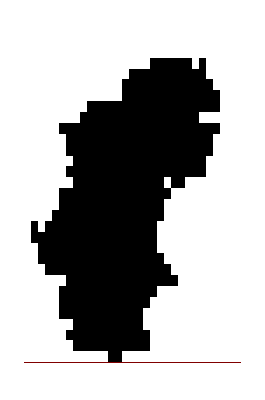
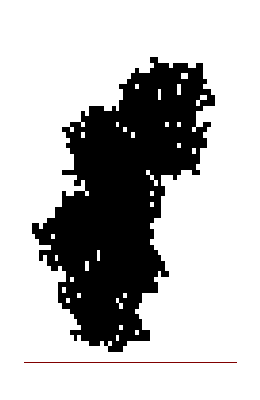
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[#, ColorRules->Automatic]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, pro1, UpTo[Ceiling[# / divs]]&/@ Dimensions[pro1]]]]/@ Table[2^n, {n,2, 8}])
```

```mathematica
EntityClass["Protein","BiologicalProcesses"->MemberQ["NeuronDifferentiation"]]//EntityList
```

{plasma membrane calcium ATPase 2 isoform 1,cyclin-dependent kinase 5,sphingosine-1-phosphate receptor 1,ephrin receptor EphA2,empty spiracles homeobox 2,GATA binding protein 2,homeo box HB9,T-cell leukemia homeobox 1,homeobox C8,neurogenin 1,nuclear receptor subfamily 4, group A, member 2,Brn3b POU domain transcription factor,mitogen-activated protein kinase kinase 1,tubulin, beta 2,superiorcervical ganglia, neural specific 10,BR serine/threonine kinase 1,CCAAT/enhancer binding protein beta,empty spiracles homolog 1,inhibitor of DNA binding 3,LIM homeobox transcription factor 1, beta,reticulon 1 isoform A,SWI/SNF-related matrix-associated actin-dependent regulator of chromatin a1 isoform a,B-cell translocation gene 2,N-ethylmaleimide-sensitive factor attachment protein, alpha,LIM domain binding 1 isoform 3,BR serine/threonine kinase 2,tubulin, beta, 4,neugrin, neurite outgrowth associated isoform 1,B-cell translocation gene 4,neurogenin 2,myotrophin,proprotein convertase subtilisin/kexin type 9 preproprotein,BarH-like homeobox 2,tubulin, beta 2B}

```mathematica
Length[]
```

34

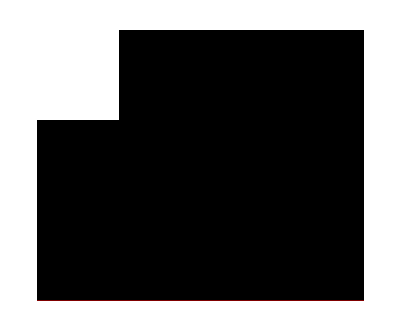
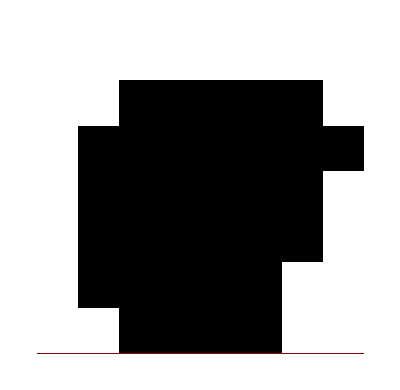
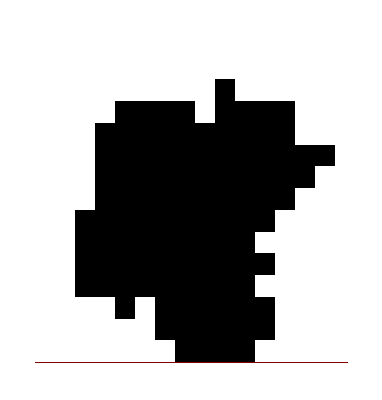
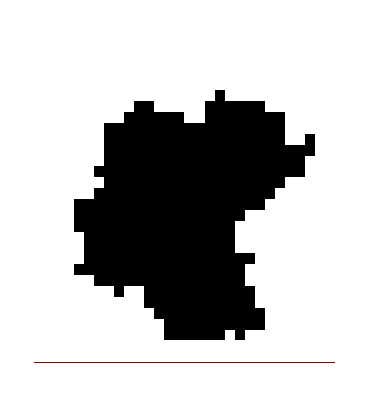
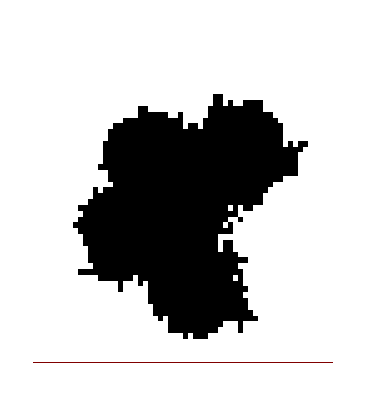
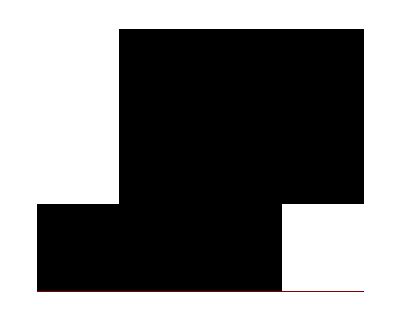
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ArrayPlot[#, ColorRules->Automatic]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 8}])&/@ (ImageData[Binarize[#]]&)/@DeleteMissing[(#[EntityProperty["Protein","WireframeDiagram"]]&/@)]
```

```mathematica
ArrayPlot[#, ColorRules->Automatic]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 8}])&/@ (ImageData[Binarize[#]]&)/@DeleteMissing[(#[EntityProperty["Protein","WireframeDiagram"]]&/@RandomSample[EntityList["Protein"],100])]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
DeleteMissing[(#[EntityProperty["Protein","WireframeDiagram"]]&/@RandomSample[EntityList["Protein"],100])]
```

{-Graphics-}

```mathematica
InputForm[EntityProperty["Protein","WireframeDiagram"]]
```

EntityProperty["Protein", "WireframeDiagram"]

```mathematica
#["WireframeDiagram"]&/@RandomSample[EntityList["Protein"],100]
```

{Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],-Graphics-,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],-Graphics-,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],-Graphics-,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],-Graphics-,Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable],Missing[NotAvailable]}

```mathematica
ParallelMap[DeleteMissing[(#[EntityProperty["Protein","WireframeDiagram"]]&/@RandomSample[EntityList["Protein"],100])]
```

```mathematica
SeedRandom[333222];ps = ParallelSelect[RandomSample[EntityList["Protein"],1000], #[EntityProperty["Protein","WireframeDiagram"]]=!=Missing["NotAvailable"]&];
```

```mathematica
ArrayPlot[#, ColorRules->Automatic]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,3, 8}])&/@ (ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps)
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

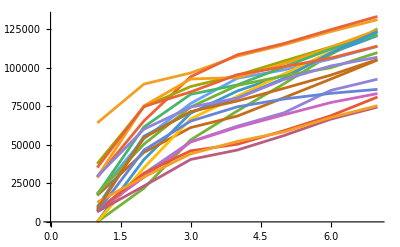

```mathematica
ListLinePlot[Count[#, 0, {2}]&/@(Function[divs, ArrayFlatten[BlockMap[ConstantArray[Boole[Max[#]>= 1], Dimensions[#]]&, #, UpTo[Ceiling[# / divs]]&/@ Dimensions[#]]]]/@ Table[2^n, {n,2, 8}])&/@ (ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps)]
```

### Making contour plot for proteins

```mathematica
(ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps)[[;;3]]
```

```mathematica
ArrayPad[{{1, 1}, {1, 1}}, 1]
```

{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}}

```mathematica
sizes=Dimensions/@;
maxDims=Max/@Transpose[sizes];
```

```mathematica
evenPad[arrays_]:=
Module[{sizes = Dimensions/@ arrays, maxDims},
maxDims = Max/@Transpose[sizes];
Module[{dims,pad},dims=Dimensions[#];
pad=Floor[(maxDims-dims)/2];(*equal pad before*)extra=maxDims-dims-pad;(*remaining pad after*)ArrayPad[#,Transpose@{pad,extra},0]]&/@arrays] ;
```

```mathematica
centeredArrays=evenPad[];
```

```mathematica
Dimensions/@ centeredArrays
```

{{430,360},{430,360},{430,360}}

```mathematica
Dimensions/@
```

{{397,360},{408,360},{430,360}}

```mathematica
ResourceFunction["ArrayCropPad"][]
```

[]

```mathematica
idata = evenPad[(ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps)];
```

```mathematica
Dimensions/@
```

{{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360},{432,360}}

```mathematica
ListContourPlot[Reverse@Map[Total[#]&,Transpose[(ImageData[Binarize[#[EntityProperty["Protein","WireframeDiagram"]]]]&/@ ps)[[;;1]],{3,1,2}],{2}]]
```

-Graphics-

```mathematica
ListContourPlot[Reverse@Map[Total[#]&,Transpose[idata,{3,1,2}],{2}]]
```

-Graphics-

```mathematica
Blend[[[All, -1]]]
```

-Graphics-

#### TODO make orientation all aligned

```mathematica
normalizeShape[array_]:=Module[{coords,com,centered,u,s,v,aligned,mask},coords=Position[array,1];(*Get coordinates of 1s*)com=Mean[coords];(*Center of mass*)centered=coords-com;(*Shift to origin*){u,s,v}=SingularValueDecomposition[N@centered];(*Principal axes*)aligned=centered.v;(*Rotate to align*)(*Shift to positive quadrant and rasterize*)mask=ConstantArray[0,Ceiling[Max[aligned]-Min[aligned]]+{1,1}];
Do[With[{r=Round[aligned[[i]]-Min[aligned]]+1},mask[[Sequence@@r]]=1],{i,Length[aligned]}];
mask];
```

```mathematica
ClearAll[normalizeShape];normalizeShape[array_]:=Module[{coords,com,mat,v,aligned,min,shifted,dims,mask},(*Get coordinates of 1s*)coords=Position[array,1];
(*Center coordinates*)com=Mean[coords];
mat=N[coords-com];
(*PCA alignment via SVD*){_,_,v}=SingularValueDecomposition[mat];
aligned=mat.v;
(*Shift to positive quadrant*)min=Floor[Min/@Transpose[aligned]];
shifted=Round[aligned-min]+1;
(*Build new binary mask*)dims=Max/@shifted;
mask=ConstantArray[0,dims];
Do[mask[[Sequence@@shifted[[i]]]]=1,{i,Length[shifted]}];
mask];
```

```mathematica
ClearAll[normalizeShape];normalizeShape[array_]:=Module[{(*coords,com,centered,mat,v,aligned,min,shifted,dims,mask*)},coords=Position[array,1];
com=Mean[coords];
(*subtract com from each coordinate*)centered=(#-com&)/@coords;
mat=N[centered];(*now an n×2 numeric matrix*)(*PCA alignment via SVD*){_,_,v}=SingularValueDecomposition[mat];
aligned=mat.v;(*still n×2*)(*shift into positive quadrant*)min=Floor[Min/@Transpose[aligned]];
shifted=Round[aligned-min]+1;(*list of integer {i,j} pairs*)(*rasterize back into a 2D binary mask*)dims=Max/@shifted;
mask=ConstantArray[0,dims];
Do[mask[[Sequence@@shifted[[i]]]]=1,{i,Length[shifted]}];
mask
];
```

```mathematica
mat
```

{}

```mathematica
masks=idata[[All,All,1]];    (*this is a List of nImages many 2D arrays*)
```

```mathematica
coords
```

```mathematica
com
```

{716995/3472,70993/372}

```mathematica
mat
```

```mathematica
normalizeShape/@idata[[;;1]]
```

Set::nosym: _ does not contain a symbol to attach a rule to.

Thread::tdlen: Objects of unequal length in {{154.965,-28.9},{153.966,-28.945},{152.922,-27.9909},{151.923,-28.0359},{150.879,-27.0819},«41»,{138.945,-6.59799},{138.405,5.38987},{138.36,6.38886},{138.27,8.38683},«10366»}+«1» cannot be combined.

Thread::tdlen: Objects of unequal length in {161,140}+{{154.965,-28.9},{153.966,-28.945},{152.922,-27.9909},{151.923,-28.0359},{150.879,-27.0819},«42»,{138.405,5.38987},{138.36,6.38886},{138.27,8.38683},«10366»} cannot be combined.

Set::pkspec1: The expression {161,140}+{{154.965,-28.9},{153.966,-28.945},{152.922,-27.9909},{151.923,-28.0359},{150.879,-27.0819},«42»,{138.405,5.38987},{138.36,6.38886},{138.27,8.38683},«10366»} cannot be used as a part specification.

{1}

### Trying with cells